```mathematica
PRACTICAL 1
```

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→C[1][y/x]}}

```mathematica
pde=D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x/3]+C[2][t+x/3]}}

```mathematica
PRACTICAL 2
```

```mathematica
pde=2*D[u[x,y],x]+3*D[u[x,y],y]==2*x*y;
sol=DSolve[{pde,u[0,y]==y^2},u[x,y],{x,y}]
Plot3D[u[x,y]/.sol,{x,-3,3},{y,-4,4},AxesLabel-> {x,y,u}]
```

{{u[x,y]→1/4 (9 x^2-x^3-12 x y+2 x^2 y+4 y^2)}}

-Graphics3D-

```mathematica
PRACTICAL 3
```

```mathematica
pde=x*D[u[x,y],x]+(x+y)*D[u[x,y],y]==u[x,y]+1;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→-1+x C[1][(y-x Log[x])/x]}}

```mathematica
f0=ContourPlot3D[(u+1)/x,{u,0,1},{x,0.1,0.2},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x","y","u"}];
f1=ContourPlot3D[(y-x*Log[x])/x,{u,0,1},{x,0.1,0.2},{y,0,1},ImageSize-> {250,250},AxesLabel-> {"x,","y","z"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

```mathematica
PRACTICAL 4
```

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

```mathematica
da[c_,f_,g_,x_,t_]:=
1/2((f/.x-> x+c*t)+(f/.x-> x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[1,Sin[x],Cos[x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel-> {t,x,u}]
```

Cos[x] Sin[t]+1/2 (-Sin[t-x]+Sin[t+x])

-Graphics3D-

```mathematica
PRACTICAL 5
```

```mathematica
eqn={D[u[x,t],t]==1/2*D[u[x,t],{x,2}],u[x,0]==(Sin[x])^2,u[0,t]==0,u[π,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,π},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,π},{t,0,4},AxesLabel->{u,t,x}]
```

-Graphics3D-

```mathematica
PRACTICAL 6
```

```mathematica
eqn={D[u[x,t],{t,2}]-9*D[u[x,t],{x,2}]==0,u[x,0]==0,Derivative[0,1][u][x,0]==x^3,Derivative[1,0][u][0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,4},AxesLabel-> {"t","x","u"},Ticks-> {{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

```mathematica
PRACTICAL 7 (Part 1)
```

```mathematica
The characteristic base curve for the given initial value problem are given by:
```

```mathematica
charBaseCurves1=DSolve[{x'[t]==x[t]*Sin[t],x[0]==x0},x[t],t]
```

{{x[t]→ⅇ^(1-Cos[t]) x0}}

{5 ⅇ^(1-Cos[t]),10 ⅇ^(1-Cos[t]),15 ⅇ^(1-Cos[t]),20 ⅇ^(1-Cos[t])}

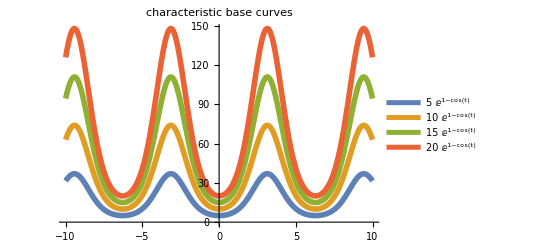

```mathematica
tab=Table[x[t]/.charBaseCurves1[[1]]/.{x0-> k},{k,5,20,5}]
Plot[Evaluate[tab],{t,-10,10},PlotStyle-> Thickness[0.01],PlotLegends-> Table[tab[[i]],{i,1,4}],PlotLabel-> "characteristic base curves"]
```

```mathematica
The Traffic Density function ρ(x,t) or the solution for the given initial value problem are given by:
```

```mathematica
eqn1=D[ρ[x,t],t]+x*Sin[t]*D[ρ[x,t],x]==0;
sol1=DSolve[{eqn1,ρ[x,0]==1 + 1/(1+x^2)},ρ[x,t],{x,t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[x,t]→(2 ⅇ^2+ⅇ^(2 Cos[t]) x^2)/(ⅇ^2+ⅇ^(2 Cos[t]) x^2)}}

```mathematica
Hence ρ(x,t) is the traffic density function of the given initial value problem:
```

```mathematica
Plot3D[ρ[x,t]/.sol1,{x,-10,10},{t,-10,10},PlotLabel-> "Traffic Density Function"]
```

-Graphics3D-

```mathematica
PRACTICAL 7 (Part 2)
```

```mathematica
The characteristic base curve for the given initial value problem are given by:
```

```mathematica
charBaseCurves2=DSolve[{x'[t]==Exp[t],x[0]==x0},x[t],t]
```

{{x[t]→-1+ⅇ^t+x0}}

{3+ⅇ^t,7+ⅇ^t,11+ⅇ^t,15+ⅇ^t,19+ⅇ^t}

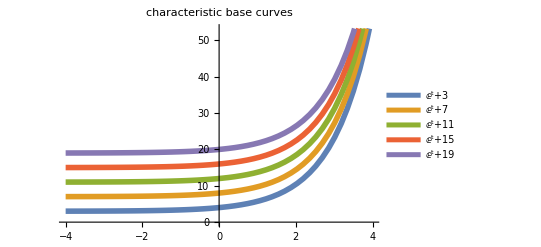

```mathematica
tab=Table[x[t]/.charBaseCurves2[[1]]/.{x0-> k},{k,4,20,4}]
Plot[Evaluate[tab],{t,-4,4},PlotStyle-> Thickness[0.01],PlotLegends-> Table[tab[[i]],{i,1,5}],PlotLabel-> "characteristic base curves"]
```

```mathematica
The Traffic Density function ρ(x,t) or the solution for the given initial value problem are given by:
```

```mathematica
eqn2=D[ρ[x,t],t]+Exp[t]*D[ρ[x,t],x]==2ρ[x,t];
sol2=DSolve[{eqn2,ρ[x,0]==1 + Sin[x]*Sin[x]},ρ[x,t],{x,t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[x,t]→ⅇ^(2 t) (1+Sin[1-ⅇ^t+x]^2)}}

```mathematica
Hence ρ(x,t) is the traffic density function of the given initial value problem:
```

```mathematica
Plot3D[ρ[x,t]/.sol2,{x,-4,4},{t,-1,1},PlotLabel-> "Traffic Density Function"]
```

-Graphics3D-